Q1
(A)

```mathematica
a=-3;
b=10;
n1=255;
Θ=Subdivide[0,π,n1]//N;
Z=-Cos[Θ];
X=(a+b)/2+(b-a)/2 Z; (*Chebyshev-Gauss-Lobatto nodes*)
```

```mathematica
Subscript[Dn, nn_][Xgrid_]:=NDSolve`FiniteDifferenceDerivative[Derivative[nn],Xgrid,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
```

```mathematica
PseudoSpectralProgram[x_, y_, z_] := Module[{X=x, Y=y},d=Subscript[Dn, z][X];d.N[Y]];
```

(B)

```mathematica
F[x_] = Sin[3x];
```

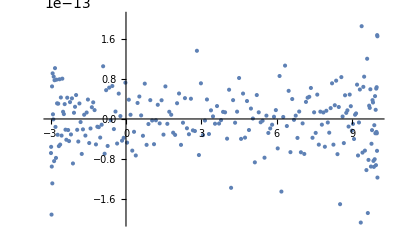

```mathematica
ListPlot[Transpose[{X,PseudoSpectralProgram[X, F[X], 1]  - F'[X]}]]
```

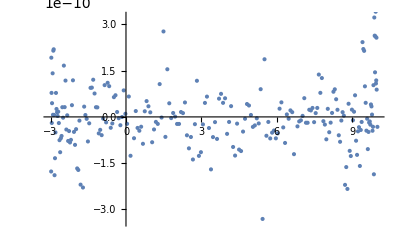

```mathematica
ListPlot[Transpose[{X,PseudoSpectralProgram[X, F[X], 2] - F''[X]}]]
```

(C)

```mathematica
XNew[nn_] := (a+b)/2 + -Cos[N[Subdivide[0,π,nn]]]*((b-a)/2);
```

```mathematica
errorlist = ConstantArray[0.,{20}];
stepsize = ConstantArray[0.,{20}];
```

```mathematica
For[i=1;t=16,i<=20,i++,t=t +4;errorlist[[i]] = Total[Abs[PseudoSpectralProgram[XNew[t-1],F[XNew[t-1]],2] -  N[F''[XNew[t-1]]]]]]
For[i=1 ; t=16,i<=20,i++,t=t+2; stepsize[[i]] = t-1]
```

```mathematica
numericalapprox = ListPlot[Transpose[{stepsize,Log10[errorlist]}],PlotStyle->Green, PlotLabels->"numerical_approx"]
```

-Graphics-

Q2 
(A)

```mathematica
V[x_, y_] = 1/2(x^2+2 y^2);
```

```mathematica
F[t_,{q1_,q2_,p1_,p2_}]={p1,p2,-D[V[q1,q2], q1],-D[V[q1,q2], q2]};
```

```mathematica
-D[V[q1,q2], q2]
```

-2 q2

```mathematica
n1=1000;
h=100./n1;
T=Subdivide[0,100,n1]//N;
U=ConstantArray[{0,0,1.,1.},n1+1];
```

```mathematica
Do[K1=h*F[T[[i]],U[[i]]];   (*dU/dt*)
K2=h*F[T[[i]]+h/2,U[[i]]+K1/2];
U[[i+1]]=U[[i]]+K2,
{i,1,n1}]
```

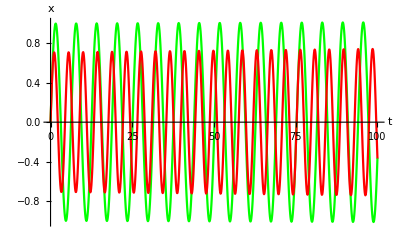

```mathematica
ListPlot[Transpose[{T,U[[All,1]]}], AxesLabel-> {"t", "x"}, Joined->True, PlotStyle->Green];
ListPlot[Transpose[{T,U[[All,2]]}], AxesLabel-> {"t", "y"}, Joined->True, PlotStyle->Red];
Show[%%,%]
```

```mathematica
ListLinePlot3D[Transpose[{U[[All,1]], U[[All,2]],T}], AxesLabel-> {"x", "y","t"}]
```

-Graphics3D-

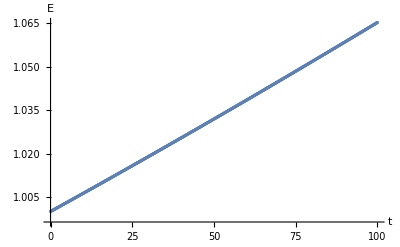

```mathematica
ListPlot[Transpose[{T,(1/2)*(U[[All,3]]^2+U[[All,4]]^2) + (1/2)*(U[[All,1]]^2+2 U[[All,2]]^2)}],AxesLabel->{"t","E"}]
```

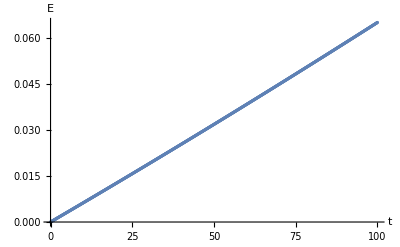

```mathematica
ListPlot[Transpose[{T,(1/2)*(U[[All,3]]^2+U[[All,4]]^2) + (1/2)*(U[[All,1]]^2+2 U[[All,2]]^2)-(1/2)*(U[[1,3]]^2+U[[1,4]]^2) + (1/2)*(U[[1,1]]^2+2 U[[1,2]]^2)}],AxesLabel->{"t","E"}]
```

(C)

```mathematica
n1=1000;
h=100./n1;
T=Subdivide[0,100,n1]//N;
U=ConstantArray[{0,0,1.,1.},n1+1];
L={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-2,0,0}};
I2 = IdentityMatrix[4];
Btrap = Inverse[I2-h/2 L ].(h*L );
```

```mathematica
Do[U[[i+1]]=U[[i]]+ Btrap.U[[i]],
{i,1,n1}]
```

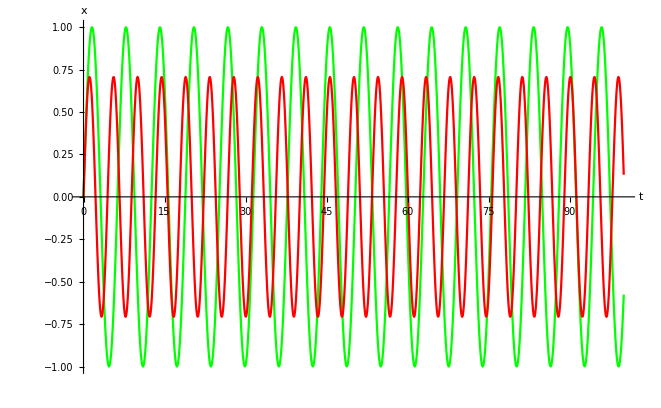

```mathematica
ListPlot[Transpose[{T,U[[All,1]]}], AxesLabel-> {"t", "x"}, Joined->True, PlotStyle->Green];
ListPlot[Transpose[{T,U[[All,2]]}], AxesLabel-> {"t", "y"}, Joined->True, PlotStyle->Red];
Show[%%,%]
```

```mathematica
ListLinePlot3D[Transpose[{U[[All,1]], U[[All,2]],T}], AxesLabel-> {"x", "y","t"}]
```

-Graphics3D-

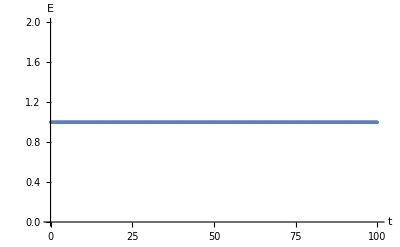

```mathematica
ListPlot[Transpose[{T,(1/2)*(U[[All,3]]^2+U[[All,4]]^2) + (1/2)*(U[[All,1]]^2+2 U[[All,2]]^2)}],AxesLabel->{"t","E"}]
```

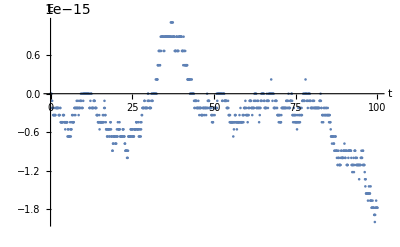

```mathematica
ListPlot[Transpose[{T,(1/2)*(U[[All,3]]^2+U[[All,4]]^2) + (1/2)*(U[[All,1]]^2+2 U[[All,2]]^2)-(1/2)*(U[[1,3]]^2+U[[1,4]]^2) + (1/2)*(U[[1,1]]^2+2 U[[1,2]]^2)}],AxesLabel->{"t","E"}]
```

Q3
(A)

```mathematica
a=.
b=.
t=.
x=.
f[x_] = ⅇ^(-a(b+t-Log[1-x])^2);
```

```mathematica
D[f[x], t] - (1-x)D[f[x], x]
```

0

(B)

```mathematica
a=0;
b=1;
n1=255;
Θ=Subdivide[0,π,n1]//N;
Z=-Cos[Θ];
X=(a+b)/2+(b-a)/2 Z; (*Chebyshev-Gauss-Lobatto nodes*)
Δx=X[[2]]-X[[1]];
```

```mathematica
(*Clenshaw-Curtis quadrature weights for integration*)
n=n1;
If[Mod[n,2]==0,W=2/n(1-Cos[n Θ]/(n^2-1)-∑_(k=1)^(n/2-1) (2Cos[2k Θ])/(4 k^2-1));
W[[1]]=1./(n^2-1);W[[-1]]=W[[1]];,
W=2/n(1-∑_(k=1)^((n-1)/2) (2Cos[2k Θ])/(4 k^2-1));W[[1]]=1./n^2;W[[-1]]=W[[1]];]
W=W*(b-a)/2;
```

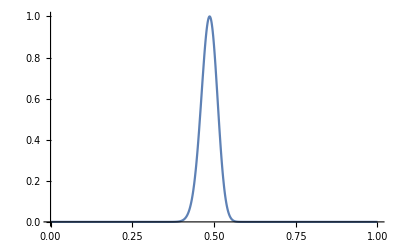

```mathematica
f[x_,t_]=If[Abs[x]<1.,If[-218*(-2/3+t-Log[1-x])^2<-583,0.,ⅇ^(-218*(-2/3+t-Log[1-x])^2)],0.];
df[x_]=If[Abs[x]<1.,If[-218/9 (2+3 Log[1-x])^2<-583,0.,-(436 ⅇ^(-218/9 (2+3 Log[1-x])^2) (2+3 Log[1-x]))/(3 (-1+x))],0.];
SetAttributes[f,Listable]
SetAttributes[df,Listable]
Plot[f[x,0],{x,a,b},PlotRange->All]
```

```mathematica
D1=NDSolve`FiniteDifferenceDerivative[Derivative[1],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
```

```mathematica
F[t_,u_]:=(1-X)*D1.u;
```

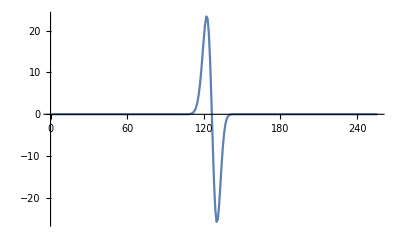

-Graphics-

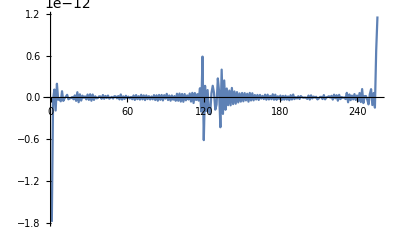

```mathematica
ListPlot[D1.f[X,0],PlotRange->All,Joined->True]
ListPlot[df[X],PlotRange->All,Joined->True]
ListPlot[D1.f[X,0]-df[X],PlotRange->All,Joined->True]
```

```mathematica
m1=100000; for pseudospectral;
tend = 1;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
U=ConstantArray[0.,{m1+1,n1+1}];       (*Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
U[[1,All]]=f[X,0];
```

```mathematica
Δt/Δx
```

0.26354

```mathematica
(*RK4 method*)
Do[K1=Δt*F[T[[ν]],U[[ν]]];   (*dU/dt=F(t,U)*)
K2=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K1/2];
K3=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K2/2];
K4=Δt*F[T[[ν]]+Δt,U[[ν]]+K3];
U[[ν+1]]=U[[ν]]+(K1+2K2+2K3+K4)/6,
{ν,1,m1}]
```

```mathematica
Manipulate[ListPlot[Transpose[{X,f[X,T[[ν]]]}],PlotRange->All,Joined->True,InterpolationOrder->3],{ν,1,m1+1}]
```

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

ListPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {{1,X},{2,f[X,T⟦1.⟧]}}.

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

ListPlot::ioproc: {{0.,If[-218. (-0.666667+Part[«2»])^2<-583.,0.,2.71828^(-218. (-0.666667+Part[«2»])^2)]},{0.0000379449,If[-218. (-0.666629+Part[«2»])^2<-583.,0.,2.71828^(-218. (-0.666629+Part[«2»])^2)]},«7»,{0.00307043,If[-218. (-0.663592+Part[«2»])^2<-583.,0.,2.71828^(-218. (-0.663592+Part[«2»])^2)]},«246»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

```mathematica
Manipulate[Show[ListPlot[Transpose[{X,f[X,T[[ν]]]}],PlotRange->All,Joined->True,InterpolationOrder->3],
ListPlot[Transpose[{X,U[[ν]]}],PlotRange->All,Joined->False]],{ν,1,m1+1}]
```

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«502»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«502»}}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«502»}}],PlotRange→All,Joined→False]].

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

ListPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {{1,X},{2,f[X,T⟦1.⟧]}}.

Part::partd: Part specification U⟦1.⟧ is longer than depth of object.

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

ListPlot::ioproc: {{0.,If[-218. (-0.666667+Part[«2»])^2<-583.,0.,2.71828^(-218. (-0.666667+Part[«2»])^2)]},{0.0000379449,If[-218. (-0.666629+Part[«2»])^2<-583.,0.,2.71828^(-218. (-0.666629+Part[«2»])^2)]},«7»,{0.00307043,If[-218. (-0.663592+Part[«2»])^2<-583.,0.,2.71828^(-218. (-0.663592+Part[«2»])^2)]},«246»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

Part::partd: Part specification U⟦1.⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},U⟦1.⟧} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},U⟦1.⟧}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},U⟦1.⟧}],PlotRange→All,Joined→False]].

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{«1»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},«1»}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,«22»,«22»,0.00185817,0.00242654,0.00307043,«246»},{«1»}}],«1»,Joined→«5»]].

```mathematica
Manipulate[ListPlot[Transpose[{X,f[X,T[[ν]]]-U[[ν]]}],PlotRange->All,Joined->True,InterpolationOrder->3],{ν,1,m1+1}]
```

Thread::tdlen: Objects of unequal length in {-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«246»}+{96.8889,96.8779,96.8448,96.7896,96.7125,96.6133,96.4921,96.349,96.184,95.9971,«502»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«246»}+{96.8889,96.8779,96.8448,96.7896,96.7125,96.6133,96.4921,96.349,96.184,95.9971,«502»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«246»}+{96.8889,96.8779,96.8448,96.7896,96.7125,96.6133,96.4921,96.349,96.184,95.9971,«502»}}] is not a list of numbers or pairs of numbers.

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

Part::partd: Part specification U⟦1.⟧ is longer than depth of object.

ListPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {{1,X},{2,f[X,T⟦1.⟧]-1. U⟦1.⟧}}.

Thread::tdlen: Objects of unequal length in {8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,«23»,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«246»}+«1» cannot be combined.

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{«1»}+«1»} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},«1»}] is not a list of numbers or pairs of numbers.

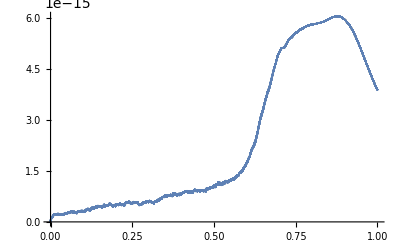

```mathematica
l1=Table[W.Abs[U[[ν]]-f[X,T[[ν]]]],{ν,1,m1+1}];
ListPlot[Transpose[{T,l1}]]
```

(C)

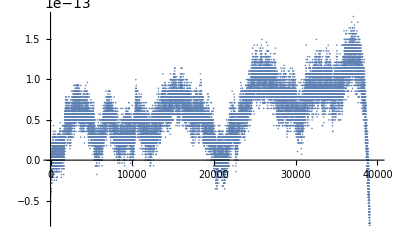

```mathematica
En2=Table[W.((1-X)*(D1.U[[ν]])^2),{ν,1,m1+1-60000}];
ListPlot[En2-En2[[1]]]
```

(D)

```mathematica
m1=100000; for pseudospectral;
tend =1;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
U=ConstantArray[0.,{m1+1,n1+1}];       (*Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
U[[1,All]]=f[X,0];
I2 = IdentityMatrix[256];
L = (1-X)*D1;
BHerm = Inverse[I2-Δt/2*L + Δt^2/12*MatrixPower[L,2] ].(Δt*L );
```

```mathematica
Do[U[[i+1]]=U[[i]]+ BHerm.U[[i]],
{i,1,m1}]
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{X,f[X,T[[ν]]]}],PlotRange->All,Joined->True,InterpolationOrder->3],
ListPlot[Transpose[{X,U[[ν]]}],PlotRange->All,Joined->False]],{ν,1,m1+1}]
```

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«502»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«502»}}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«502»}}],PlotRange→All,Joined→False]].

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

ListPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {{1,X},{2,f[X,T⟦1.⟧]}}.

Part::partd: Part specification U⟦1.⟧ is longer than depth of object.

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

ListPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {{1,X},{2,f[X,T⟦1.⟧]}}.

Part::partd: Part specification U⟦1.⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,1.09995×10^-42,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«502»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,1.09995×10^-42,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«502»}}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,1.09995×10^-42,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«502»}}],PlotRange→All,Joined→False]].

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{«1»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},«1»}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,«22»,«22»,0.00185817,0.00242654,0.00307043,«246»},{«1»}}],«1»,Joined→«5»]].

```mathematica
Manipulate[ListPlot[Transpose[{X,f[X,T[[ν]]]-U[[ν]]}],PlotRange->All,Joined->True,InterpolationOrder->3],{ν,1,m1+1}]
```

Thread::tdlen: Objects of unequal length in {-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«246»}+{96.8889,96.8779,96.8448,96.7896,96.7125,96.6133,96.4921,96.349,96.184,95.9971,«502»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«246»}+{96.8889,96.8779,96.8448,96.7896,96.7125,96.6133,96.4921,96.349,96.184,95.9971,«502»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{-96.8889,-96.8779,-96.8448,-96.7896,-96.7125,-96.6133,-96.4921,-96.349,-96.184,-95.9971,«246»}+{96.8889,96.8779,96.8448,96.7896,96.7125,96.6133,96.4921,96.349,96.184,95.9971,«502»}}] is not a list of numbers or pairs of numbers.

Part::partd: Part specification T⟦1⟧ is longer than depth of object.

Part::partd: Part specification U⟦1⟧ is longer than depth of object.

ListPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {{1,X},{2,f[X,T⟦1⟧]-1. U⟦1⟧}}.

Thread::tdlen: Objects of unequal length in {8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,1.09995×10^-42,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«246»}+{-8.35007×10^-43,-8.44268×10^-43,-8.72667×10^-43,-9.2213×10^-43,-9.96102×10^-43,-1.09995×10^-42,-1.24164×10^-42,-1.43267×10^-42,-1.68973×10^-42,-2.03698×10^-42,«502»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,1.09995×10^-42,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«246»}+{-8.35007×10^-43,-8.44268×10^-43,«8»,«502»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,1.09995×10^-42,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«246»}+{-8.35007×10^-43,-8.44268×10^-43,«8»,«502»}}] is not a list of numbers or pairs of numbers.

Thread::tdlen: Objects of unequal length in {8.35007×10^-43,8.44268×10^-43,8.72667×10^-43,9.2213×10^-43,9.96102×10^-43,«23»,1.24164×10^-42,1.43267×10^-42,1.68973×10^-42,2.03698×10^-42,«246»}+«1» cannot be combined.

Transpose::nmtx: The first two levels of {{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},{«1»}+«1»} cannot be transposed.

ListPlot::lpn: Transpose[{{0.,0.0000379449,0.000151774,0.00034147,0.000607004,0.000948336,0.00136541,0.00185817,0.00242654,0.00307043,«246»},«1»}] is not a list of numbers or pairs of numbers.

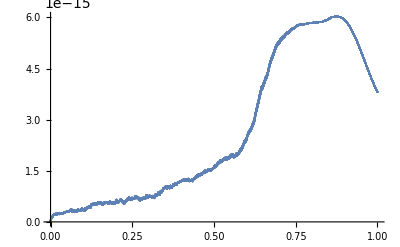

```mathematica
l1=Table[W.Abs[U[[ν]]-f[X,T[[ν]]]],{ν,1,m1+1}];
ListPlot[Transpose[{T,l1}]]
```

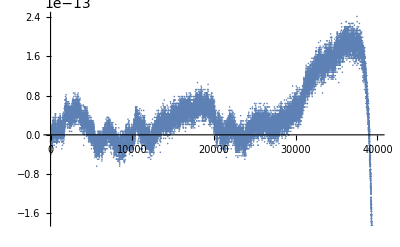

```mathematica
En2=Table[W.((1-X)*(D1.U[[ν]])^2),{ν,1,m1+1-60000}];
ListPlot[En2-En2[[1]]]
```

Part B 
Question 6
A

```mathematica
a=.
b=.
t=.
x=.
ψ[t_,x_] = ⅇ^(-a*(b+t-Log[1-x])^2)
```

ⅇ^(-a (b+t-Log[1-x])^2)

```mathematica
-(1+x)*D[ψ[t,x], {t,2}] + (1-2x^2)*(D[D[ψ[t,x], {t,1}], {x,1}]) + (1-x)*x^2*D[ψ[t,x], {x,2}]-2x*D[ψ[t,x], {t,1}]+x(2-3x)*D[ψ[t,x], {x,1}]//Simplify
```

0

```mathematica
D[ψ, t]==π
D[π, t]==((1-2 x^2)D[π, x]+(1-x)x^2 D[ψ, xx] - 2xπ  + x(2-3x)D[ψ, x])/(1+x)
```

False

0==-(2 xπ)/(1+x)

```mathematica
L1 = ((1-x)x^2 D2  + x(2-3x)D1)/(1+x);
L2 =  ((1-2 x^2)D1  + 2xI)/(1+x) ;
```

(B)

```mathematica
a=0;
b=1;
n1=255;
Θ=Subdivide[0,π,n1]//N;
Z=-Cos[Θ];
X=(a+b)/2+(b-a)/2 Z; (*Chebyshev-Gauss-Lobatto nodes*)
Δx=X[[2]]-X[[1]];
```

-Graphics-

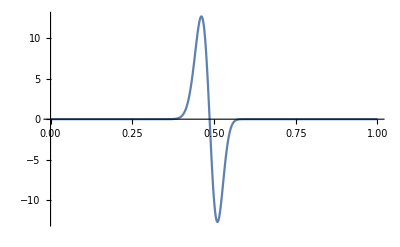

```mathematica
(*Clenshaw-Curtis quadrature weights for integration*)
n=n1;
If[Mod[n,2]==0,W=2/n(1-Cos[n Θ]/(n^2-1)-∑_(k=1)^(n/2-1) (2Cos[2k Θ])/(4 k^2-1));
W[[1]]=1./(n^2-1);W[[-1]]=W[[1]];,
W=2/n(1-∑_(k=1)^((n-1)/2) (2Cos[2k Θ])/(4 k^2-1));W[[1]]=1./n^2;W[[-1]]=W[[1]];]
W=W*(b-a)/2;

f[x_,t_]=If[Abs[x]<1.,If[-218*(-2/3+t-Log[1-x])^2<-583,0.,ⅇ^(-218*(-2/3+t-Log[1-x])^2)],0.];
df[x_]=If[Abs[x]<1.,If[-218/9 (2+3 Log[1-x])^2<-583,0.,-436 ⅇ^(-218 (-2/3-Log[1-x])^2) (-2/3-Log[1-x])],0.];
SetAttributes[f,Listable]
SetAttributes[df,Listable]
Plot[f[x,0],{x,a,b},PlotRange->All]
Plot[df[x],{x,a,b},PlotRange->All]
```

```mathematica
D1=NDSolve`FiniteDifferenceDerivative[Derivative[1],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
D2=NDSolve`FiniteDifferenceDerivative[Derivative[2],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
```

```mathematica
(ONN=ConstantArray[0.,{n1+1,n1+1}])//N;
(INN=IdentityMatrix[n1+1])//N;
  (L1 = ((1-X)*X^2/(1+X))*D2 + (X*(2-3X)/(1+X))*D1 )//N;
(L2 = ((1-2 X^2)/(1+X))*D1  - (2X/(1+X))*INN)//N;
```

```mathematica
L2N2N=ArrayFlatten[{{ONN,INN},{L1,L2}}];
L2N2N = Developer`ToPackedArray[L2N2N, Real];
(*dU/dt=F(t,U)=L.U *)
F[t_,u_]:=L2N2N.u
```

```mathematica
L = L2N2N;
L2 = L.L;
L3 = L2.L;
L4 = L3.L;
M = (IdentityMatrix[Length[L2N2N]] +Δt*L + Δt^2/(2!)*L2 + Δt^3/(3!)*L3+Δt^4/(4!)*L4);
M = Developer`ToPackedArray[M, Real];
```

```mathematica
m1=100000;
tend = 1;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
U=ConstantArray[0.,{m1+1,2n1+2}];      (*Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
U[[1,1;;n1+1]]=f[X,0];
U[[1,n1+2;;-1]]=df[X];
U = Developer`ToPackedArray[U, Real];
```

```mathematica
Do[U[[it+1, All]] = M.U[[it,All]] , {it, 1 , m1 -1}]
```

```mathematica
(*RK4 method*)
Do[K1=Δt*F[T[[ν]],U[[ν]]];   (*dU/dt=F(t,U)*)
K2=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K1/2];
K3=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K2/2];
K4=Δt*F[T[[ν]]+Δt,U[[ν]]+K3];
U[[ν+1]]=U[[ν]]+(K1+2K2+2K3+K4)/6,
{ν,1,m1}]
```

```mathematica
ψ=U[[All,1;;n1+1]];
p=U[[All,n1+2;;-1]];
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{X,f[X,T[[ν]]]}],PlotRange->All,Joined->True,InterpolationOrder->3],
ListPlot[Transpose[{X,ψ[[ν]]}],PlotRange->All, Joined->False]],{ν,1,m1+1}]
```

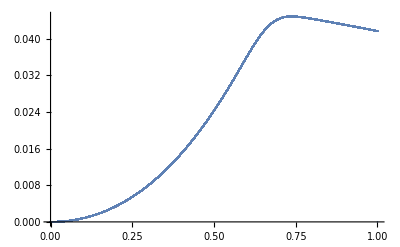

```mathematica
l1=Table[W.Abs[ψ[[ν]]-f[X,T[[ν]]]],{ν,1,m1+1}];
ListPlot[Transpose[{T,l1}]]
```

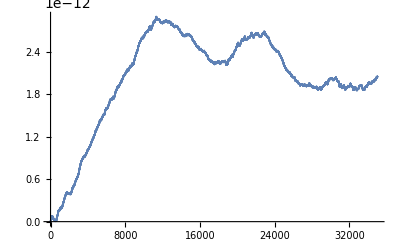

```mathematica
En2=Table[W.((1+X)*(p[[ν]])^2+X^2*(1-X)*(D1.ψ[[ν]])^2),{ν,1,m1-65000}];
ListPlot[En2-En2[[1]]]
```

```mathematica
L = L2N2N;
```

```mathematica
m1=1000;
tend = 1;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
U=ConstantArray[0.,{m1+1,2n1+2}];      (*Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
U[[1,1;;n1+1]]=f[X,0];
U[[1,n1+2;;-1]]=df[X];
U = Developer`ToPackedArray[U, Real];
```

```mathematica
BHerm = Inverse[IdentityMatrix[Length[L2N2N]] -Δt/2*L + Δt^2/12*MatrixPower[L,2] ].(Δt*L ); 
BHerm = Developer`ToPackedArray[BHerm, Real];
```

```mathematica
Do[U[[i+1]]=U[[i]]+ BHerm.U[[i]],
{i,1,m1}]
```

```mathematica
ψ=U[[All,1;;n1+1]];
p=U[[All,n1+2;;-1]];       (*Subscript[π, i]^ν=π(Subscript[t, ν],Subscript[x, i])*)
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{X,f[X,T[[ν]]]}],PlotRange->All,Joined->True,InterpolationOrder->3],
ListPlot[Transpose[{X,ψ[[ν]]}],PlotRange->All, Joined->False]],{ν,1,m1+1}]
```

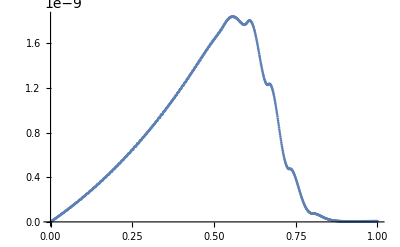

```mathematica
l1=Table[W.Abs[ψ[[ν]]-f[X,T[[ν]]]],{ν,1,m1+1}];
ListPlot[Transpose[{T,l1}]]
```

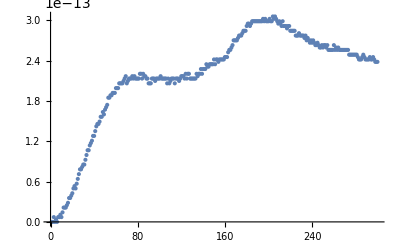

```mathematica
En2=Table[W.((1+X)*(p[[ν]])^2+X^2*(1-X)*(D1.ψ[[ν]])^2),{ν,1,m1-700}];
ListPlot[En2-En2[[1]]]
```

```mathematica
V[l_,s_] = l(l+1)-(s-X)(1+s);
```

```mathematica
(ONN=ConstantArray[0.,{n1+1,n1+1}])//N;
(INN=IdentityMatrix[n1+1])//N;
  (L1 = ((1-X)*X^2/(1+X))*D2 + (X*(2-3X)/(1+X))*D1 - V[2,0]*INN )//N;
(L2 = ((1-2 X^2)/(1+X))*D1  - (2X/(1+X))*INN)//N;
```

```mathematica
L2N2N=ArrayFlatten[{{ONN,INN},{L1,L2}}];
L2N2N = Developer`ToPackedArray[L2N2N, Real];
(*dU/dt=F(t,U)=L.U *)
F[t_,u_]:=L2N2N.u
```

```mathematica
L = L2N2N;
```

```mathematica
m1=1000;
tend = 1;
Δt=tend/m1;
T=Subdivide[0,tend,m1]//N;
U=ConstantArray[0.,{m1+1,2n1+2}];      (*Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
U[[1,1;;n1+1]]=f[X,0];
U[[1,n1+2;;-1]]=df[X];
U = Developer`ToPackedArray[U, Real];
```

```mathematica
BHerm = Inverse[IdentityMatrix[Length[L2N2N]] -Δt/2*L + Δt^2/12*MatrixPower[L,2] ].(Δt*L ); 
BHerm = Developer`ToPackedArray[BHerm, Real];
```

```mathematica
Do[U[[i+1]]=U[[i]]+ BHerm.U[[i]],
{i,1,m1}]
```

```mathematica
ψ=U[[All,1;;n1+1]];
p=U[[All,n1+2;;-1]];
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{X,f[X,T[[ν]]]}],PlotRange->All,Joined->True,InterpolationOrder->3],
ListPlot[Transpose[{X,ψ[[ν]]}],PlotRange->All, Joined->False]],{ν,1,m1+1}]
```